```mathematica
(*** Fixed Points and Nullclines ***)
```

```mathematica
(* Toggle Switch with double self activation *)
f[x_,y_]:=gA*(A0A^nAA/(A0A^nAA+x^nAA)+(λAA*x^nAA)/(A0A^nAA+x^nAA))*(B0A^nBA/(B0A^nBA+y^nBA)+(λBA*y^nBA)/(B0A^nBA+y^nBA))-γA*x;g[x_,y_]:=gB*(B0B^nBB/(B0B^nBB+y^nBB)+(λBB*y^nBB)/(B0B^nBB+y^nBB))*(A0B^nAB/(A0B^nAB+x^nAB)+(λAB*x^nAB)/(A0B^nAB+x^nAB))-γB*y;
```

{{x→-226.264,y→-226.264},{x→212.096,y→21.7199},{x→21.7199,y→212.096},{x→137.67,y→96.0896},{x→96.0896,y→137.67},{x→119.281,y→119.281}}

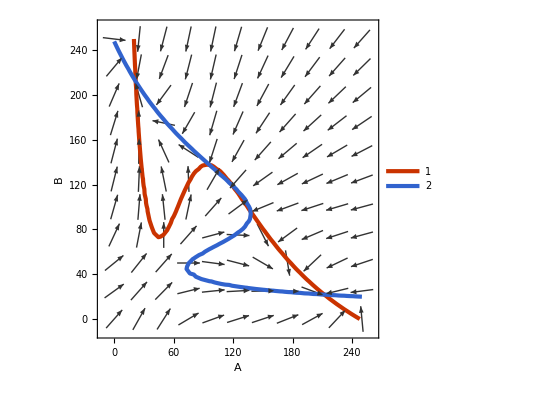

```mathematica
(* TSSA - Tristable Parameter Set 1 *)
gA=5; gB=5; (* production rates *)
γA=0.1; γB=0.1; (* degradation rates *)
B0A=120; A0B=120; (* Threshold *)
A0A=80; B0B=80; (* Threshold *)
nBA=1; nAB=1; (* Hill-coefficient *)
nAA=4; nBB=4; (* Hill-coefficient *)
λBA=0.1;λAB=0.1;
λAA=5;λBB=5;
S=NSolve[{f[x,y]==0,g[x,y]==0},{x,y},Reals]
vp=VectorPlot[{f[x,y],g[x,y]},{x,0,250},{y,0,250},VectorPoints->11,VectorStyle->{GrayLevel[0.2]},VectorScale->{0.065,0.9,None}];cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,0,250},{y,0,250},PlotTheme-> "Web",ContourStyle->Directive[AbsoluteThickness[3]],Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,10],Axes-> True,BoundaryStyle->Black];
Show[vp,cp,FrameLabel->{{HoldForm[B],None},{HoldForm[A],None}},PlotLabel->None,LabelStyle->{20,GrayLevel[0],Bold},Axes->True,AxesStyle->Black]
```

{{x→-278.334,y→-278.334},{x→216.796,y→25.8761},{x→25.8761,y→216.796},{x→188.106,y→56.8925},{x→56.8925,y→188.106},{x→138.473,y→138.473}}

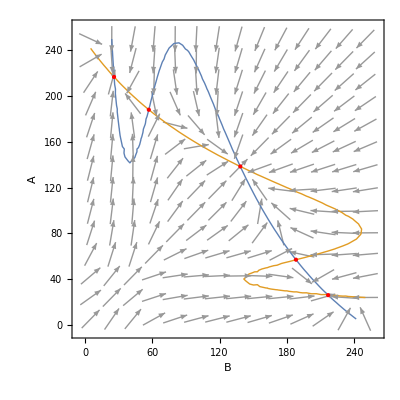

```mathematica
(* TSSA : another (extra) tristable parameter set *)
gA=5; gB=5; (* production rates *)
γA=0.1; γB=0.1; (* degradation rates *)
B0A=160; A0B=160; (* Threshold *)
A0A=70; B0B=70; (* Threshold *)
nBA=1; nAB=1; (* Hill-coefficient *)
nAA=4; nBB=4; (* Hill-coefficient *)
λBA=0.1;λAB=0.1;
λAA=5;λBB=5;
NSolve[{f[x,y]==0,g[x,y]==0},{x,y},Reals]
vp=VectorPlot[{f[x,y],g[x,y]},{x,5,250},{y,5,250},VectorScale->{0.065,0.9,None},VectorPoints->14,VectorStyle->{GrayLevel[0.6]}];cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,5,250},{y,5,250},PlotTheme-> "Default",ContourStyle->Thick,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,10],Axes-> True,BoundaryStyle->Black];
ptRules=NSolve[{f[x,y]==0,g[x,y]==0},{x,y},Reals];
Show[vp,cp,Graphics[{Red,PointSize[Large],Point[{x,y}]/.ptRules}],FrameLabel->{{HoldForm[A],None},{HoldForm[B],None}},PlotLabel->None,LabelStyle->{14,GrayLevel[0],Bold},Axes->True,AxesStyle->Black]
```